# Structural Properties and Results

Quotient Process

Coverings

## Quotients from Equitable Partition

```mathematica
grassman1=PermutationGroup[{
Cycles[{{1,2},{3,4}}],
Cycles[{{1,3},{2,4}}],
Cycles[{{1,4},{2,3}}]
}];
cover=CompleteGraph[6,VertexSize->0.3, VertexLabels->Table[i -> i, {i, 1, 6}]];
highlightCover = HighlightGraph[cover, CompletePartition[cover, GroupOrbits[grassman1]]];
orbigraph1=OrbigraphFromGroup[cover, grassman1];
orbigraph1 = SetProperty[orbigraph1, {VertexSize->.2,VertexShapeFunction-> {1->"Square", 2-> "Triangle", 3->"Star"}, VertexStyle->{1-> Red, 2->Yellow, 3->Purple}}];

Column[{
PaneSelector[
{
1 -> Style["What is a covering graph?","Subsection"],
2-> Style["What is an equitable partition?", "Subsection"], 
3-> Style["How do we quotient?","Subsection"]
},
Dynamic[time],
ImageSize->Full, 
TransitionEffect->"Fade",
 Alignment->Center]
Slider[Dynamic[time], {1, 3, 1}],
PaneSelector[{1 -> cover,2-> highlightCover, 3-> Grid[{{highlightCover, Spacer[100],orbigraph1}}, ItemSize->Full]},Dynamic[time],ImageSize->Full, TransitionEffect->"Fade", Alignment->Center]
},Center, ItemSize->Automatic]
```

## Universal Covering Tree

### What is a universal covering tree?

```mathematica
OrbigraphVertexWeight[orbi_Graph, v_] := Total[WeightedAdjacencyMatrix[orbi]⟦v⟧];

(* Expands a single vertex into all of its appropriate neighbors*)
ExpandCoveringVertex[tree_, v_,orbi_,styles_, types_, idx_] :=
Module[{add, t = tree,tps = types, i = idx, di = VertexDegree[tree, v], dsts = Flatten[Position[orbi⟦types[v]⟧,x_/;x> 0], 1]},
Return[
{
(
{t, tps, i} = ExpandCoveringVertexType[t,v, orbi, styles, #, tps, i];
)&/@dsts;
t,
tps,
i
}
]
]

OrbigraphStyles[orbi_Graph] := {PropertyValue[{orbi, #}, VertexShapeFunction], PropertyValue[{orbi, #}, VertexStyle]} &/@ VertexList@orbi;

OrbigraphTypeTable[orbi_Graph] := Module[{types},
(types[#] = #)&/@(VertexList@orbi);
Return[types]
]

ExtendUniversalCovering[tree_Graph, orbi_,styles_, types_, k_Integer] := Module[{t = tree, idx = Max[VertexList[tree]] + 1, ot = types, toextend=Select[VertexList[tree], VertexDegree[tree,#] < k &]},
(
		{t, ot, idx} = ExpandCoveringVertex[t, #, orbi, styles, ot, idx];
)&/@toextend;
	Return[{t, ot}];
];

(* Expands all the neighbors of a particular type*)
ExpandCoveringVertexType[tree_, v_, orbi_, styles_, type_, types_,idx_]:=
(* 
To find the number of vertices needed, simply look at total required of this type,
then subtract off the total number of vertices of that type already connected
*)
Block[{ts = types, tr = tree, needed = orbi⟦types[v], type⟧ - Length@Select[AdjacencyList[tree, v], types[#] == type&] },
{
(
ts[#] = type;
tr = EdgeAdd[tr, v <->#];
tr = SetProperty[{tr, #},VertexShapeFunction-> First@styles⟦type⟧];
tr = SetProperty[{tr, #},VertexStyle-> Last@styles⟦type⟧];
)&/@ Range[idx, idx + needed - 1]; 
tr,
ts,
idx + needed
}
]

PartialUniversalCovering[orbi_Graph, d_Integer] := Block[
{
k=OrbigraphVertexWeight[orbi, First@VertexList@orbi],
types = OrbigraphTypeTable[orbi],
styles = OrbigraphStyles[orbi],
adj =  Normal@WeightedAdjacencyMatrix@orbi
},
Block[{init = Graph[{1}, {},ImageSize-> {900, 500},VertexShapeFunction->{1 -> First@First@styles}, VertexStyle->{1 -> Last@First@styles},GraphLayout ->  "RadialEmbedding"]},
First@Nest[
ExtendUniversalCovering[First@#,adj,styles, Last@#, k]&,{init, types}, d]
]
]

sizes = PartialUniversalCovering[orbigraph1, #]&/@Range[4];

GraphPlotRange[graph_Graph] := With[{embedding = GraphEmbedding@graph},
{{Min[First /@ embedding]-1, Max[First/@embedding]+1},{Min[Last/@embedding]-1, Max[Last/@embedding]+1}}]

biggest = Last@sizes;
sizes =SetProperty[#, {VertexCoordinates-> Take[GraphEmbedding@Last@sizes, VertexCount@#],PlotRange-> GraphPlotRange[biggest]}]&/@sizes;
ListAnimate[sizes, DefaultDuration->3]
```

## Good and Bad Orbigraphs

What’s a good orbigraph?

What’s a bad orbigraph?

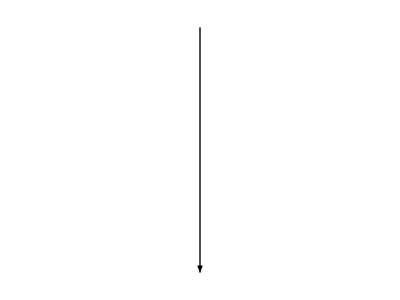
| Good Orbigraph | Bad Orbigraph | 
 | -Graphics- | -Graphics- | 
 | -Graphics- | -Graphics- | 
 | -Graphics- | 𝓍 | 
 | -Graphics- | -Graphics- | 
 | -Graphics- | -Graphics- |

```mathematica
badOrbi = SetProperty[
AdjacencyOrbigraph[{{0,2,1},{1,0,2},{2,1,0}}],
{
VertexSize -> .1,
VertexStyle->
{
1 -> Red,
2-> Yellow,
3->Purple
},
VertexShapeFunction->
{
1-> "Triangle",
2->"Square",
3->"Star"
}
}
];

goodOrbi = SetProperty[
AdjacencyOrbigraph[{{0,3},{1,2}}],
{
VertexSize->.1,
VertexStyle->
{
1-> Red, 
2-> Yellow
},
 VertexShapeFunction->
{
1-> "Triangle", 
2-> "Square"
}
}
];

goodCover = ColorGraph@WeightedAdjacencyMatrix@goodOrbi;

dwnArrw = Graphics[{Arrowheads[.1],Arrow[{{0,.3},{0,-.3}}]}];
goodUCover = SetProperty[PartialUniversalCovering[goodOrbi,4], ImageSize->Automatic];
badUCover = SetProperty[PartialUniversalCovering[badOrbi,4], ImageSize->Automatic];

Grid[
{

{
Spacer[5],
Style["Good Orbigraph", "Subsection"]
,
Style["Bad Orbigraph", "Subsection"],
Spacer[5]
},

{
Spacer[5],
goodUCover,
badUCover,
Spacer[5]
},

{
Spacer[5],
dwnArrw,
dwnArrw,
Spacer[5]
},

{
Spacer[5],
goodCover,
Magnify[Text[Style["𝓍", Red, 24]], 4],
Spacer[5]
},
{
Spacer[5],
dwnArrw,
dwnArrw,
Spacer[5]
},
{
Spacer[5],
goodOrbi,
badOrbi,
Spacer[5]
}
},
Alignment->{{Left, Right}},
ItemSize->{{Scaled[.2], Scaled[.3], Scaled[.3], Scaled[.2]}}
]
```

## Characterization of Good and Bad Orbigraphs

Good: No “unbalanced” cycles (Kolmogorov cycle condition)

Bad: Unbalanced cycles

```mathematica
badOrbi = SetProperty[
AdjacencyOrbigraph[{{0,2,1},{1,0,2},{2,1,0}}],
{
VertexSize -> .1,
VertexStyle->
{
1 -> Red,
2-> Yellow,
3->Purple
},
VertexShapeFunction->
{
1-> "Triangle",
2->"Square",
3->"Star"
}
}
];

goodOrbi = SetProperty[
AdjacencyOrbigraph[{{0,3},{1,2}}],
{
VertexSize->.1,
VertexStyle->
{
1-> Red, 
2-> Yellow
},
 VertexShapeFunction->
{
1-> "Triangle", 
2-> "Square"
}
}
];
dwnArrw = Graphics[{Arrowheads[.1],Arrow[{{0,.3},{0,-.3}}]}];

kolmogorov=
Manipulate[
Row[{
SetProperty[
If[d ≤ 2,
HighlightGraph[badOrbi, {
Style[
(Mod[#, 3]+1->Mod[1+#, 3]+1)&/@Range[d+1], 
Darker@Green,
Thickness[.007]
]
}
],
HighlightGraph[badOrbi, {
Style[
(Mod[#, 3]+1->Mod[1+#, 3]+1)&/@Range[3], 
Darker@Green,
Thickness[.007]
],
Style[
(Mod[5-#+1, 3]+1->Mod[5-#, 3]+1)&/@Range[d-3+1],
Darker@Red,
Thickness[.007]]
}
]
],ImageSize-> {Scaled[.50], Scaled[1.0]}],
Spacer[20],
Magnify[
Which[
d ≤ 2,
Style[StringJoin@Riffle[ConstantArray["2", d+1], "×", 2], "Subsubsection"],
d > 2,
Style[StringJoin@({"2×2×2≠"} ~Append~Riffle[ConstantArray["1", (d-3)+1], "×", 2]), "Subsubsection"]
],.90]
},
ImageSize->{350,300}
],

 {d, 0, 5,1}];

Grid[
{

{
Spacer[5],
Style["Good Orbigraph", "Subsection"],
Spacer[.2],
Style["Bad Orbigraph", "Subsection"],
Spacer[5]
},
{
Spacer[5],
goodOrbi,
Spacer[.1],
kolmogorov,
Spacer[5]
}
},
Alignment->{{Left, Right}},
ItemSize->{{Scaled[.05], Scaled[.3], Scaled[.05], Scaled[.3], Scaled[.2]}}
]
```

| Good Orbigraph |  | Bad Orbigraph | 
 | -Graphics- |  |  |

## Example: Good Orbigraph

Let’s pick a random good orbigraph and construct a covering

```mathematica
Column[{
Dynamic[Button["Generate Random Orbigraph", 
randOrbi = AdjacencyOrbigraph@GenerateRandomOrbigraph[3, 3];
While[Not[ConnectedGraphQ[randOrbi] ]|| Not[OrbigraphReversibleQ[randOrbi]],
randOrbi =AdjacencyOrbigraph@ GenerateRandomOrbigraph[3, 3];
];


randOrbi = SetProperty[
randOrbi,
{
VertexSize->.1,
VertexStyle->
{
1-> Red, 
2-> Yellow,
3->Purple
},
 VertexShapeFunction->
{
1-> "Triangle", 
2-> "Square",
3->"Star"
}
}
]
]
],
Button["Generate Finite Covering",
Dynamic[coveringGraph = SetProperty[
ColorGraph[WeightedAdjacencyMatrix@randOrbi],
{ImageSize->{300,300}, GraphLayout->"SpringEmbedding"}
];
]
],
Dynamic[coveringGraph],
dwnArrw,
Dynamic[SetProperty[randOrbi, ImageSize->{300, 100}]]
},
Alignment->Center
]
```

Generate Finite Covering

-Graphics-

## How did we discover and prove this connection?

Comes from Markov chain property: Reversibility

Detailed balance equation: π_i P_(i, j)= π_j P_(j,i)

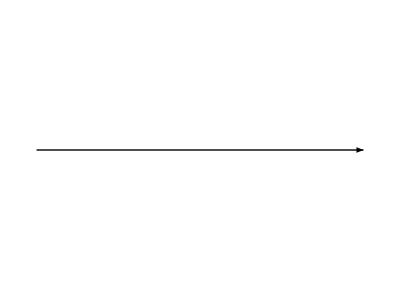

```mathematica
rightArrw = Graphics[{Arrowheads[.1],Arrow[{{-1.5,0},{1.5,0}}]}];

Row[{Dynamic[Button["Generate Random Orbigraph", 
randOrbi = AdjacencyOrbigraph@GenerateRandomOrbigraph[3, 3];
While[Not[ConnectedGraphQ[randOrbi]] || Not[OrbigraphReversibleQ[randOrbi]],
randOrbi =AdjacencyOrbigraph@ GenerateRandomOrbigraph[3, 3];
];


randOrbi = SetProperty[
randOrbi,
{
VertexSize->.1,
VertexStyle->
{
1-> Red, 
2-> Yellow,
3->Purple
},
 VertexShapeFunction->
{
1-> "Triangle", 
2-> "Square",
3->"Star"
}
}
];


markovChain =MarkovProcessFromOrbigraph@WeightedAdjacencyMatrix@randOrbi;
markovChainG =  SetProperty[Graph@markovChain, ImageSize->{300, 200}];

normalizedOrbigraph = SetProperty[randOrbi, {EdgeWeight-> N[PropertyValue[randOrbi, EdgeWeight]/3], ImageSize->{300, 200}}];

(counts[#] = 0)&/@ VertexList@markovChain;
totalCounts = 0;
]
]}
]

GenerateRandomWalk[chain_DiscreteMarkovProcess, len_Integer] :=Module[{counts ,walk= {}, cur=1,next,  G = Graph@chain, T=Normal@MarkovProcessProperties[chain, "TransitionMatrix"]},
cur = RandomChoice[VertexList@g];
counts = {ConstantArray[0, VertexCount@G]};

 For[i = 0, i < len, i++, 
next = RandomChoice[Cases[T⟦cur⟧, x_/;x ≠ 0]-> Flatten[Position[T⟦cur⟧, x_/;x ≠ 0],1]];
walk = Append[walk, next];
counts = Append[counts, Last@counts];
counts⟦Length@counts,next⟧++; 
cur = next;
];

Return[{walk, counts}];
]

w = GenerateRandomWalk[markovChain, 5000];

Row[{
Dynamic[SetProperty[randOrbi, ImageSize->{400, 100}]],
Spacer[100],
rightArrw,
Spacer[100],
Manipulate[
Row[{
HighlightGraph[normalizedOrbigraph, {Style[(First@w)⟦t⟧, Lighter@Green]}],
Spacer[20],
Pane[
Column[{
Style[StringJoin@{"π = [",Riffle[ToString@NumberForm[#,{2,2}]&/@N[(Last@w)⟦t⟧/t],", ", 2], "]"}, "Subsubsection"],
Spacer[10],
Style["π_1P_(1, 2)= π_2P_(2, 1)", "Subsubsection"],
Spacer[10],
With[{A = WeightedAdjacencyMatrix@normalizedOrbigraph},
Style[StringForm["`` = ``",
 NumberForm[((Last@w)⟦t⟧/t)⟦1⟧ * A⟦1,2⟧, {2,2}],
NumberForm[((Last@w)⟦t⟧/t)⟦2⟧ * A⟦2,1⟧, {2,2}]
],
 "Subsubsection"]
]
}
],
Alignment->Center,
ImageSize->{200, 200}
]
}
],
{t, 1, Length@First@w, 1}
]}
,
Alignment->Center
]
```